```mathematica
(*slo*)
sico={131,179,215,250,277,287,319,342,368,406,441,477,525,571,632,684,730,756,802,841,897,934,977,1009,1032,1067,1103,1136,1171,1199,1216,1223,1223+8,1223+8+28,1223+8+28+21};
dtests={1045,1197,916,590,871,1121,1026,1184,1200,872,731,1257,1240,1181,1075,1387,999,596,1125,1288,1095,1050,1188,655,489,1202,1212,1144,1234,1232,572,544,541,1168,1023,1193,1250,685};
dcases={49,48,36,35,27,10,32,23,26,38,35,36,48,46,61,52,46,26,46,39,56,37,43,20,23,35,36,33,36,28,17,7,8,27,21,36,13,13};
Length[dcases]
Length[dtests]
adtests=dcases/dtests Mean[dtests]//N
cpert=Accumulate[N[adtests]]+131
timecpert=Table[i,{i,1,Length[cpert]}];
(*sico[[-34;;]]-cpert;*)
Mean[dtests]//N
cpstartdate={2020,3,11};
sico=Accumulate[dcases]+82
timesico=Table[i,{i,1,Length[sico]}];
```

38

38

{47.3564,40.4991,39.6923,59.9121,31.3072,9.00934,31.4993,19.6189,21.8822,44.0115,48.3559,28.9245,39.0947,39.3375,57.3086,37.8639,46.5041,44.0581,41.2956,30.5807,51.6503,35.5886,36.5553,30.8381,47.5026,29.4078,29.9984,29.1331,29.4636,22.9533,30.0159,12.9956,14.9345,23.3464,20.7321,30.4762,10.5035,19.1669}

{178.356,218.856,258.548,318.46,349.767,358.776,390.276,409.895,431.777,475.788,524.144,553.069,592.164,631.501,688.81,726.674,773.178,817.236,858.531,889.112,940.762,976.351,1012.91,1043.74,1091.25,1120.65,1150.65,1179.79,1209.25,1232.2,1262.22,1275.21,1290.15,1313.5,1334.23,1364.7,1375.21,1394.37}

1009.95

{131,179,215,250,277,287,319,342,368,406,441,477,525,571,632,684,730,756,802,841,897,934,977,997,1020,1055,1091,1124,1160,1188,1205,1212,1220,1247,1268,1304,1317,1330}

```mathematica
cp0={1420.4682436753844,156.7972712988734,0.12351920906743179};
```

```mathematica
cp0=cp0-PseudoInverse[dwf[cp0,timecpert,cpert]].wf[cp0,timecpert,cpert]
```

{1505.54,196.76,0.112487}

```mathematica
{cp20,ik,ie,il}=GNiteration[cpert,cp0,timecpert]
```

{{1505.74,197.966,0.113509},4,6.64247×10^-7,38}

{1526.99,216.775,0.107719}

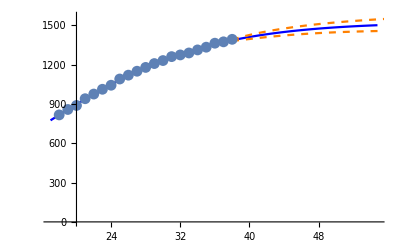
{-Graphics-,13.0982,5.43098,19.1669,-21.2983,91.3152}

```mathematica
{cp20,abctab,winds}=stepGNiteration[cpert,cp0,21,timecpert,{1,0}];
cp20
cpert20=cpert[[-21;;]];
datastats[cpert20,cp20,1.8,2,timecpert[[-21;;]]]
```

```mathematica
sip0={1384.8615587986176,145.83741820834007,0.12921631186746152};
```

```mathematica
sip0=sip0-PseudoInverse[dwf[sip0,timesico,sico]].wf[sip0,timesico,sico]
```

{1399.33,147.852,0.127407}

```mathematica
{sip0,ik,ie,il}=GNiteration[sico,sip0,timesico]
```

{{1399.8,147.909,0.127377},5,4.86396×10^-8,38}

{1439.81,183.641,0.113893}

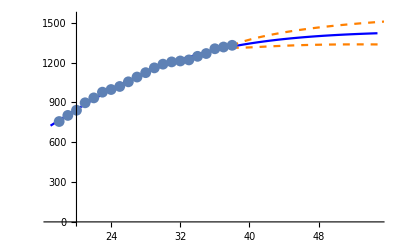
{-Graphics-,11.8745,10.2793,13,-21.1171,92.3733}

```mathematica
{sip20,abctab,winds}=stepGNiteration[sico,sip0,21,timesico,{1,0}];
sip20
sico21=sico[[-21;;]];
datastats[sico21,sip20,1.8,2,timesico[[-21;;]]]
```

```mathematica
(*italy*)
itco={3,3,9,76,124,229,322,400,650,888,1128,1679,2036,2502,3089,3858,4636,5883,7375,9172,10149,12462,15113,17660,21157,24747,27980,31506,35713,41035,47021,53578,59138,63928,69176,74386,80539,86498,92472,97689,101739,105792,110574,115242,119827,124632,128948,132547,135586,139422,143626,147577,152271,156363,159516,162488,165155,168941,172434,175925,178972};
timeitco=Table[i,{i,1,Length[itco]}];
itstartdate={2020,2,18};
```

```mathematica
ip0={174788.1382104429,823.1473098522238,0.13824837796814018};
```

```mathematica
ip0=ip0-PseudoInverse[dwf[ip0,timeitco,itco]].wf[ip0,timeitco,itco]
```

{180026.,946.992,0.133373}

```mathematica
{ip0,ik,ie,il}=GNiteration[itco,ip0,timeitco]
```

{{180026.,946.992,0.133373},1,4.51801×10^-8,61}

{224838.,7888.61,0.0763911}

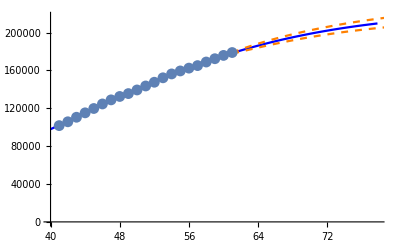
{-Graphics-,2752.22,600.376,3047,-17.6148,79.6005}

```mathematica
{itp20,abctab,winds}=stepGNiteration[itco,ip0,21,timeitco,{1,0}];
itp20
itco21=itco[[-21;;]];
datastats[itco21,itp20,1.8,2,timeitco[[-21;;]]]
```

```mathematica
avco={10,10,18,24,37,47,66,104,112,131,182,302,361,504,800,959,1132,1332,1646,1843,2649,3024,3631,4486,5282,5888,7029,7697,8291,8813,9618,10182,10711,11129,11525,11766,11983,12297,12640,12969,13248,13560,13807,13937,14043,14234,14370,14448,14603,14662};
Length[avco]
timeavco=Table[i,{i,1,Length[avco]}];
avstartdate={2020,2,29};
```

50

```mathematica
avp0={14252.234732511146,36.9115421452583,0.2140};
```

```mathematica
avp0=avp0-PseudoInverse[dwf[avp0,timeavco,avco]].wf[avp0,timeavco,avco]
```

{14333.6,38.9032,0.211793}

```mathematica
{avp0,ik,ie,il}=GNiteration[avco,avp0,timeavco]
```

{{14333.6,38.9032,0.211793},1,3.04208×10^-9,50}

{15305.,359.753,0.13691}

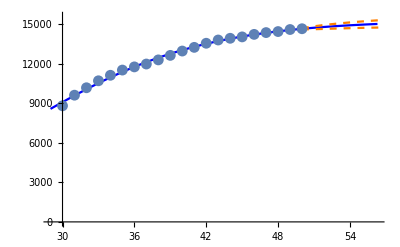
{-Graphics-,79.8351,108.972,59,-22.7797,95.7986}

```mathematica
{avp20,abctab,winds}=stepGNiteration[avco,avp0,21,timeavco,{1,0}];
avp20
avco21=avco[[-21;;]];
datastats[avco21,avp20,1.3,1,timeavco[[-21;;]]]
```

```mathematica
(*germany*)
lgerco={7,8,10,12,12,12,13,14,14,14,14,16,16,16,16,16,16,16,16,16,16,16,16,16,16,18,21,26,57,129,157,196,262,534,639,795,1112,1139,1296,1567,2369,3062,3795,4838,6012,7156,8198,10999,18323,21463,24774,29212,31554,36508,42288,48582,52547,57298,61913,67366,73522,79696,85778,91714,95391,99765,103306,108202,113525,117658,120479,123016,125098,127584,130450,133830,137439,139897,142614,144406};
lgerco=lgerco[[34;;]];
Length[lgerco]
timelgerco=Table[i,{i,1,Length[lgerco]}];
gerstartdate={2020,3,3};
```

47

```mathematica
gp0={141217.4695898566,1261.0254956584702,0.1713149345909435};
```

```mathematica
{gp0,ik,ie,il}=GNiteration[lgerco,gp0,timelgerco]
```

{{145452.,1426.39,0.165039},1,1.37282×10^-9,47}

{156152.,3713.02,0.129453}

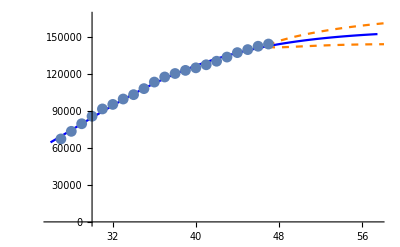
{-Graphics-,1498.69,1275.14,1792,-18.303,92.478}

```mathematica
{gp20,abctab,winds}=stepGNiteration[lgerco,gp0,21,timelgerco,{1,0}];
gp20
gerco21=lgerco[[-21;;]];
datastats[gerco21,gp20,1.5,2,timelgerco[[-21;;]]]
```

```mathematica
ameri={62,62,64,108,129,148,213,213,213,472,696,987,1264,1678,1678,1678,3503,3536,7087,10442,15219,15219,31573,42164,51914,63570,68334,85228,103321,122653,140640,163199,187302,213600,241703,273808,307318,333811,363321,395503,425889,461275,492881,524514,553822,578268,604070,632781,665781,695353,722372,751775};
Length[ameri]
ameri=ameri[[-35;;]]
timemeri=Table[n,{n,1,Length[ameri]}];
ameristartdate={2020,3,15};
```

52

{3536,7087,10442,15219,15219,31573,42164,51914,63570,68334,85228,103321,122653,140640,163199,187302,213600,241703,273808,307318,333811,363321,395503,425889,461275,492881,524514,553822,578268,604070,632781,665781,695353,722372,751775}

```mathematica
ap0={824509.9366413986,30637.964489195638,0.16684623217993633};
```

```mathematica
{ap0,ik,ie,il}=GNiteration[ameri,ap0,timemeri]
```

{{842047.,15981.9,0.165793},9,2.69672×10^-7,35}

{912505.,23774.2,0.144961}

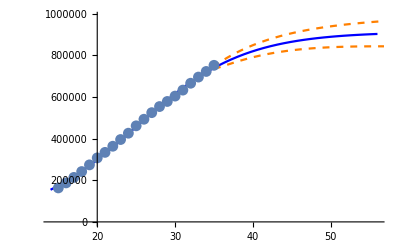
{-Graphics-,19419.2,6479.57,29403,-10.0195,82.3858}

```mathematica
{ap20,abctab,winds}=stepGNiteration[ameri,ap0,21,timemeri,{1,0}];
ap20
amer14=ameri[[-21;;]];
datastats[amer14,ap20,2,2,timemeri[[-21;;]]]
```

```mathematica
ceska={26,32,38,61,94,116,150,214,298,383,434,522,694,995,1165,1236,1394,1654,2062,2279,2663,2829,3002,3308,3589,3858,4190,4472,4822,5017,5312,5569,5732,5902,5991,6059,6141,6303,6433,6549,6654};
timeceska=Table[n,{n,1,Length[ceska]}];
ceskastartdate={2020,3,8};
```

```mathematica
cesp0={7500,100,0.16};
```

```mathematica
{cesp0,ik,ie,il}=GNiteration[ceska,cesp0,timeceska]
```

{{6830.38,77.8028,0.184278},7,7.97687×10^-7,41}

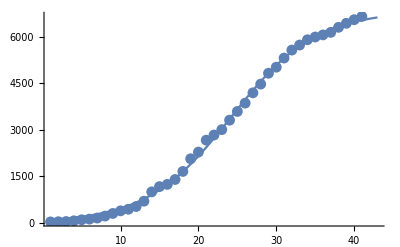

```mathematica
showplots[ceska,cesp0]
```

```mathematica
{cesp20,abctab,winds}=stepGNiteration[ceska,cesp0,21,timeceska,{1,0}];
cesp20
```

{7025.8,114.86,0.167136}

```mathematica
greece={32,32,66,73,73,89,98,98,98,228,331,331,387,418,418,495,530,624,695,743,821,892,966,1061,1156,1212,1314,1375,1514,1613,1673,1735,1755,1832,1884,1955,2011,2081,2114,2145,2170,2191,2207,2235};
timegreece=Table[n,{n,1,Length[greece]}];
greecestartdate={2020,3,6};
```

```mathematica
greecep0={2500,100,0.16};
```

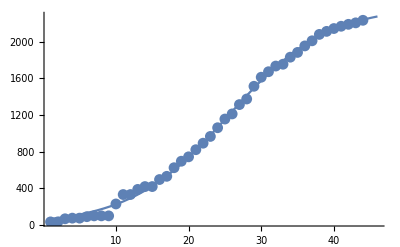

```mathematica
showplots[greece,greecep0]
```

```mathematica
{greecep0,ik,ie,il}=GNiteration[greece,greecep0,timegreece]
```

{{2380.18,55.1572,0.147159},6,5.27555×10^-7,44}

```mathematica
{greece20,abctab,winds}=stepGNiteration[greece,greecep0,21,timegreece,{1,0}];
greece20
```

{2387.08,54.1729,0.147276}

```mathematica
ice={2,9,16,26,26,45,45,55,55,61,61,61,61,138,138,199,225,250,330,409,473,568,588,648,737,802,890,963,1020,1086,1135,1220,1319,1364,1417,1486,1562,1586,1616,1648,1675,1689,1701,1711,1720,1727,1739};
ice=Drop[ice,15];
timeice=Table[n,{n,1,Length[ice]}];
icestartdate={2020,3,2+15};
```

```mathematica
icep0={2000,100,0.15};
```

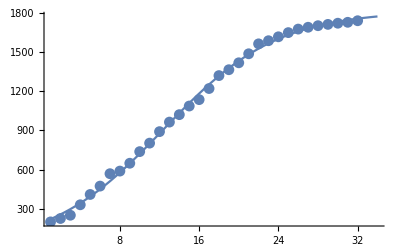

```mathematica
showplots[ice,icep0]
```

```mathematica
{icep0,ik,ie,il}=GNiteration[ice,icep0,timeice]
```

{{1813.27,188.682,0.173691},9,1.62279×10^-7,32}

```mathematica
{ice20,abctab,winds}=stepGNiteration[ice,icep0,21,timeice,{1,0}];
ice20
```

{1808.9,174.421,0.178518}

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/plotdump

{1488.04,196.169,0.114993}

{1526.99,216.775,0.107719}

{1526.99,216.775,0.107719}

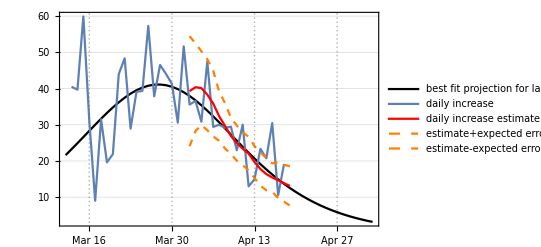
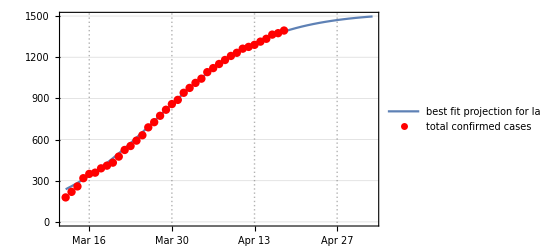
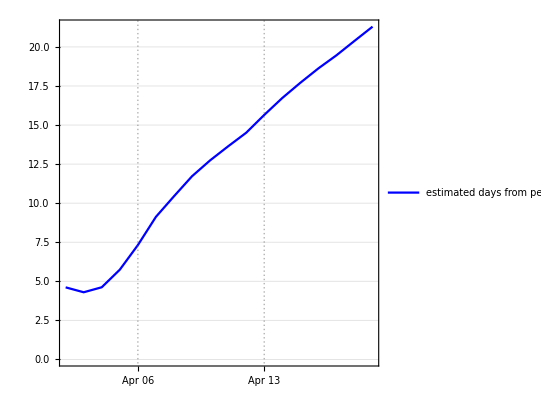
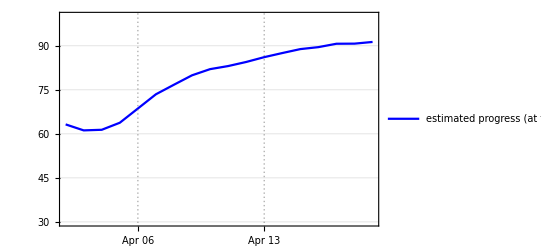

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[cp0,cp20,timecpert,cpert,cpstartdate,21,14,0]
```

```mathematica
Export["slograf.png",graf]
Export["slologgraf.png",loggraf]
Export["slodfgraf.png",dfpplot]
Export["sloprogplot.png",progplot]
datestring=reldatetostring[cpstartdate,timecpert[[-1]]];
Export["slodate.txt",datestring]
```

slograf.png

slologgraf.png

slodfgraf.png

sloprogplot.png

{23056.4,55.8783,0.276821}

{224838.,7888.61,0.0763911}

{224838.,7888.61,0.0763911}

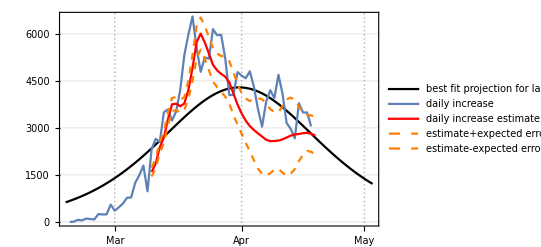
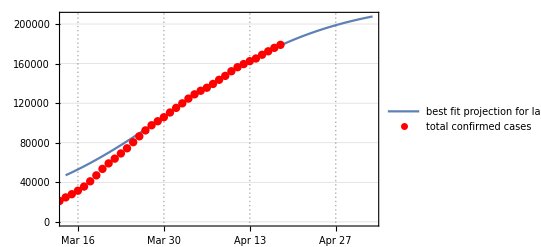
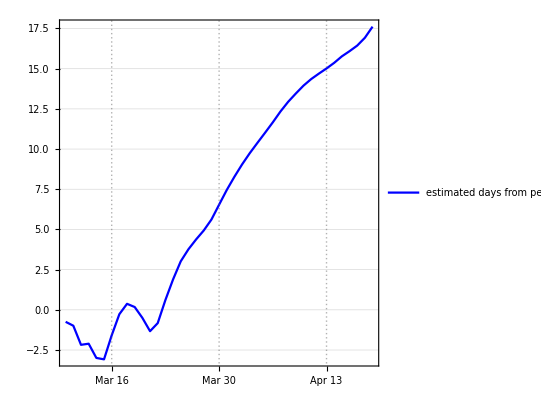
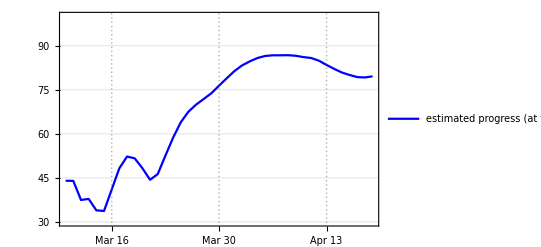

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[ip0,itp20,timeitco,itco,itstartdate,21,14,25]
```

```mathematica
Export["italygraf.png",graf]
Export["italyloggraf.png",loggraf]
Export["italydfgraf.png",dfpplot]
Export["italyprogplot.png",progplot]
datestring=reldatetostring[itstartdate,timeitco[[-1]]];
Export["italydate.txt",datestring]
```

italygraf.png

italyloggraf.png

italydfgraf.png

italyprogplot.png

italydate.txt

{9943.54,14.6999,0.258747}

{15305.,359.753,0.13691}

{15305.,359.753,0.13691}

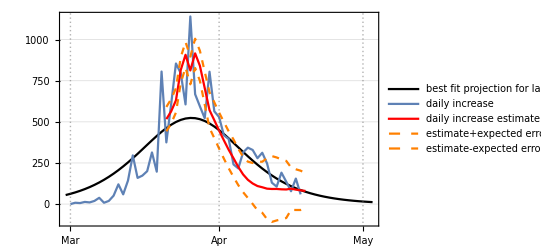
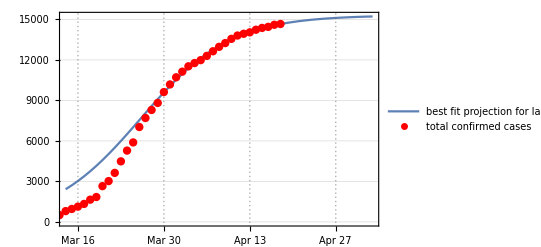
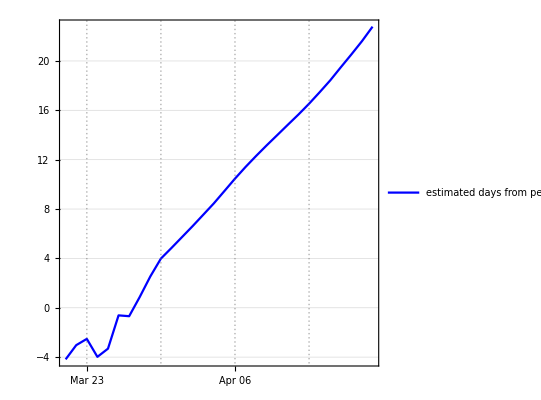
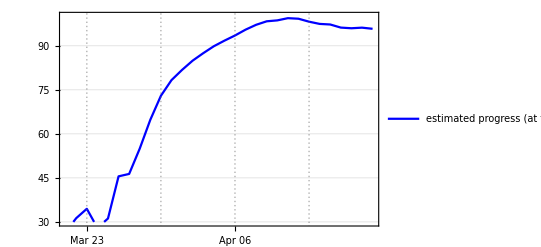

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[avp0,avp20,timeavco,avco,avstartdate,21,14,14]
```

```mathematica
Export["austriagraf.png",graf]
Export["austrialoggraf.png",loggraf]
Export["austriadfgraf.png",dfpplot]
Export["austriaprogplot.png",progplot]
datestring=reldatetostring[avstartdate,timeavco[[-1]]];
Export["austriadate.txt",datestring]
```

austriagraf.png

austrialoggraf.png

austriadfgraf.png

austriaprogplot.png

austriadate.txt

{51026.4,128.882,0.327775}

{156152.,3713.02,0.129453}

{156152.,3713.02,0.129453}

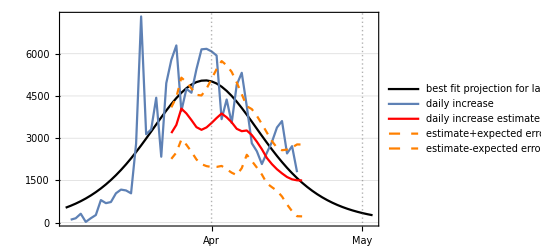
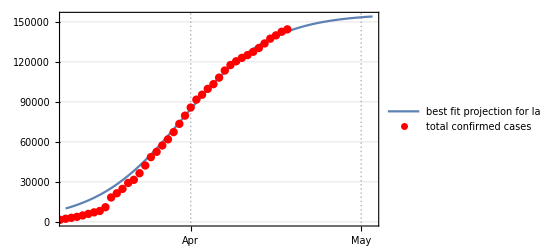
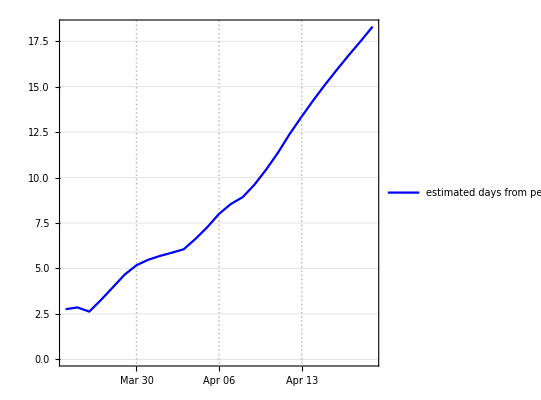
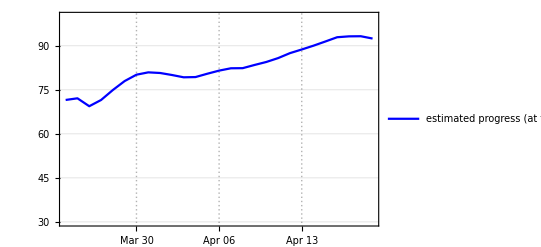

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[gp0,gp20,timelgerco,lgerco,gerstartdate,21,14,7]
```

```mathematica
Export["germangraf.png",graf]
Export["germanloggraf.png",loggraf]
Export["germandfgraf.png",dfpplot]
Export["germanprogplot.png",progplot]
datestring=reldatetostring[gerstartdate,timelgerco[[-1]]];
Export["germandate.txt",datestring]
```

germangraf.png

germanloggraf.png

germandfgraf.png

germanprogplot.png

germandate.txt

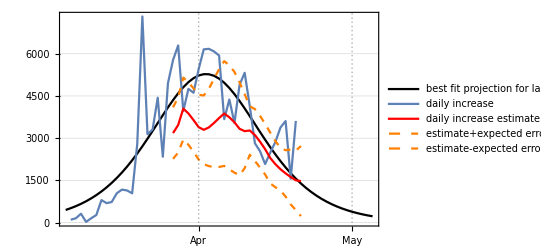

```mathematica
graf
```

{609519.,18667.,0.203405}

{827200.,29249.8,0.160815}

{827200.,29249.8,0.160815}

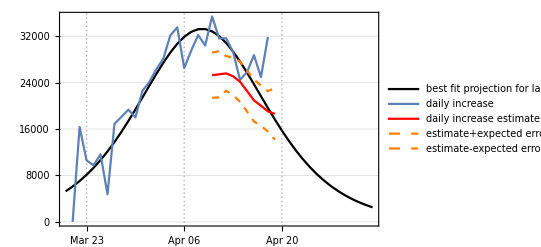
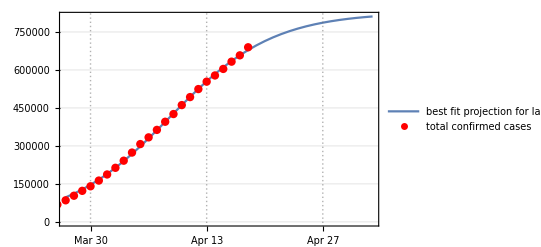
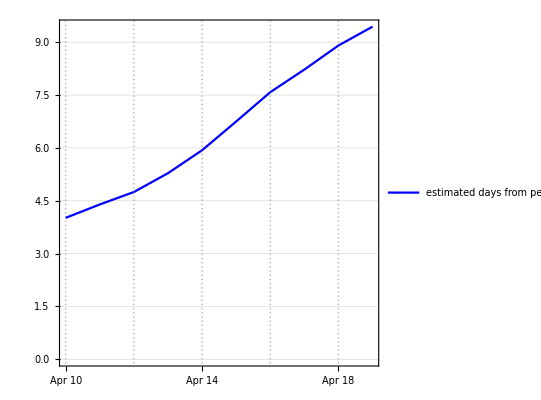
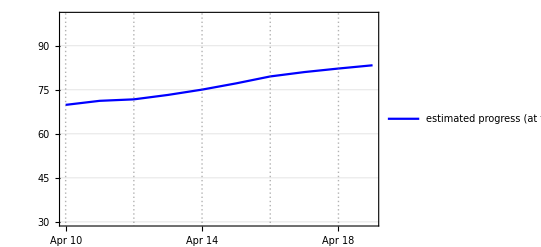

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[ap0,ap20,timemeri,ameri,ameristartdate,21,14,7]
```

{4945.17,35.6084,0.24003}

{7077.81,120.885,0.164692}

{7077.81,120.885,0.164692}

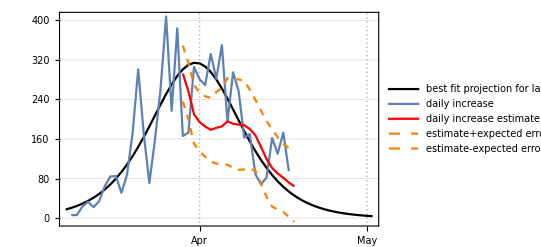
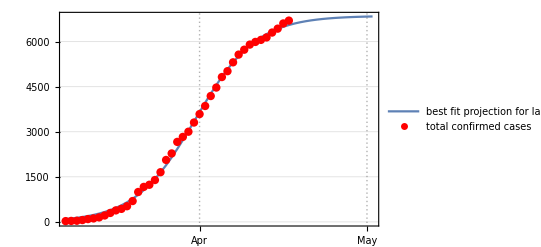
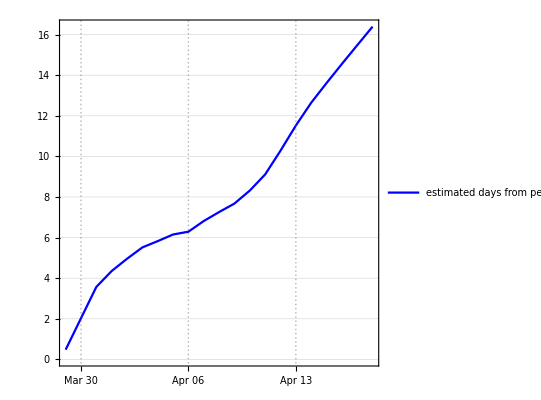
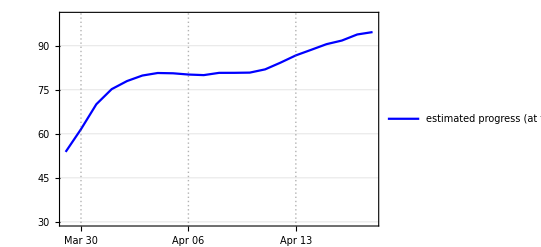

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[cesp20,cesp0,timeceska,ceska,ceskastartdate,21,14,0]
```

{1104.09,28.185,0.218766}

{2387.08,54.1729,0.147276}

{2387.08,54.1729,0.147276}

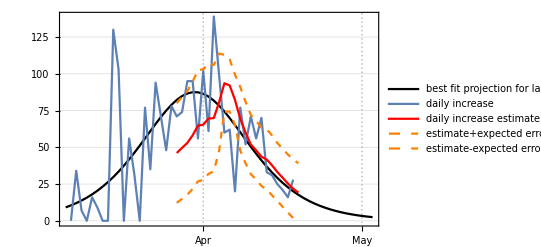
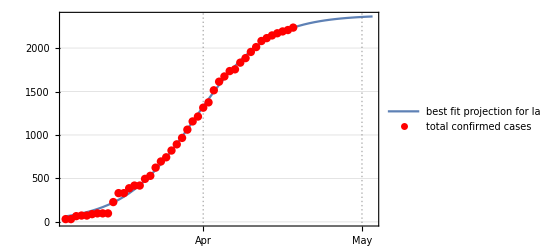
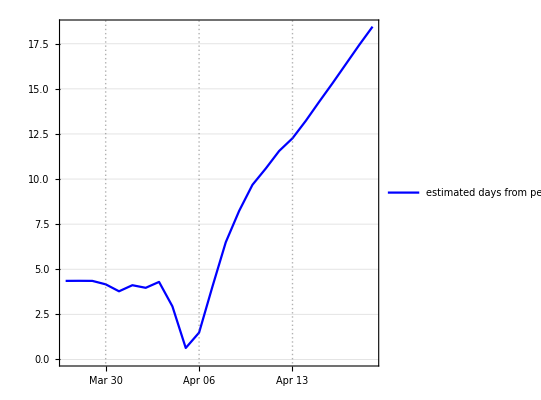
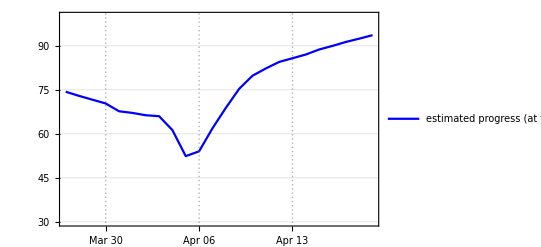

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[greece20,greecep0,timegreece,greece,greecestartdate,21,14,0]
```

{1759.23,187.527,0.17676}

{1808.9,174.421,0.178518}

{1808.9,174.421,0.178518}

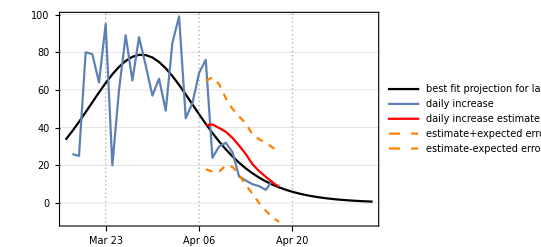
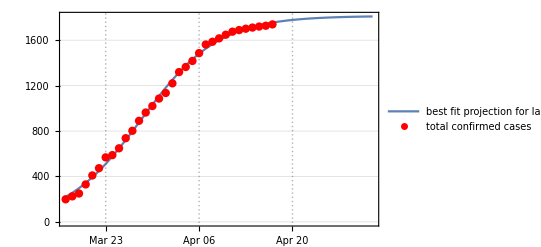
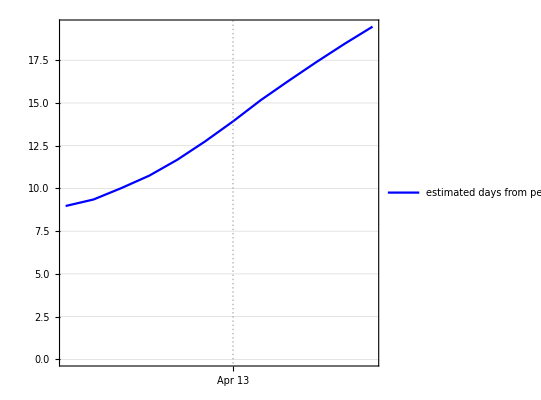
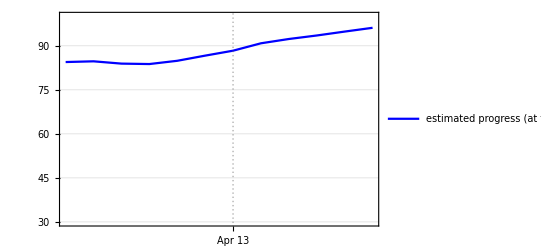

```mathematica
{graf,loggraf,dfpplot,progplot}=somegraphs[ice20,icep0,timeice,ice,icestartdate,21,14,0]
```

```mathematica
graf
```

-Graphics-